```mathematica
(*Final Code For Appendix*)

(* For Rock Paper Scissors epsilon = 0*)
eq1=r'[t]==r[t]*s[t]-r[t]*p[t];
eq2=p'[t]==p[t]*r[t]-p[t]*s[t];
eq3 = s'[t]==s[t]*p[t]-s[t]*r[t];

(*Solve the system of ODEs*)
solution = NDSolve[{eq1,eq2,eq3, r[0]==0.3,p[0]==0.4, s[0]==0.3},{r, p, s},{t,0,500}]
(*VectorPlot[Evaluate[{r[t],p[t],s[t]}/. solution],{t,0,20},PlotLegends->{"Rock","Scissors","Paper"}]*)
data=Table[Flatten@{r[t]/.solution,p[t]/.solution,s[t]/.solution},{t,0,500,0.1}];
Export["a1.txt",data,"TSV"]
solution2 = NDSolve[{eq1,eq2,eq3, r[0]==0.1,p[0]==0.8, s[0]==0.1},{r, p, s},{t,0,500}]
(*VectorPlot[Evaluate[{r[t],p[t],s[t]}/. solution],{t,0,20},PlotLegends->{"Rock","Scissors","Paper"}]*)
data2=Table[Flatten@{r[t]/.solution2,p[t]/.solution2,s[t]/.solution2},{t,0,500,0.1}];
Export["a2.txt",data2,"TSV"]
solution3 = NDSolve[{eq1,eq2,eq3, r[0]==1,p[0]==0, s[0]==0},{r, p, s},{t,0,500}]
(*VectorPlot[Evaluate[{r[t],p[t],s[t]}/. solution],{t,0,20},PlotLegends->{"Rock","Scissors","Paper"}]*)
datathree=Table[Flatten@{r[t]/.solution2,p[t]/.solution2,s[t]/.solution2},{t,0,500,0.1}];
```

{{r→InterpolatingFunction[…],p→InterpolatingFunction[…],s→InterpolatingFunction[…]}}

a1.txt

{{r→InterpolatingFunction[…],p→InterpolatingFunction[…],s→InterpolatingFunction[…]}}

a2.txt

{{r→InterpolatingFunction[…],p→InterpolatingFunction[…],s→InterpolatingFunction[…]}}

```mathematica
TernaryListPlot[{ data2, data, datathree},FrameLabel->{"R","S","P"}, Joined->True]
```

-Graphics-

```mathematica
(**********************************************)

(*Rock Paper Scissors epsilon not equal to 0*)
```

```mathematica
Clear[r, s, p]
epsilon = 0.2;
eq1=r'[t]==r[t]*(epsilon*r[t]+s[t]-p[t] - epsilon*(r[t]^2 + p[t]^2 + s[t]^2));
eq2=p'[t]==p[t]*(r[t]+epsilon*p[t]-s[t] - epsilon*(r[t]^2 + p[t]^2 + s[t]^2));
eq3 = s'[t]==s[t]*(p[t]-r[t]+epsilon*s[t]- epsilon*(r[t]^2 + p[t]^2 + s[t]^2));
r0==0.3;
p0==0.4;
s0==0.3;

(*Solve the system of ODEs*)
solution = NDSolve[{eq1,eq2,eq3, r[0]==0.3,p[0]==0.4, s[0]==0.3},{r, p, s},{t,0,500}]
(*VectorPlot[Evaluate[{r[t],p[t],s[t]}/. solution],{t,0,20},PlotLegends->{"Rock","Scissors","Paper"}]*)
data4=Table[Flatten@{r[t]/.solution,p[t]/.solution,s[t]/.solution},{t,0,500,0.1}];
Export["a4.txt",data4,"TSV"]

TernaryListPlot[{data4},FrameLabel->{"R","S","P"}, Joined->True,Epilog->{Red,PointSize@Large,Point[{0.3, 0.4, 0.3}]}]
```

{{r→InterpolatingFunction[…],p→InterpolatingFunction[…],s→InterpolatingFunction[…]}}

a4.txt

-Graphics-

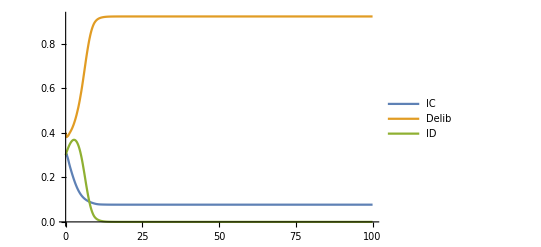

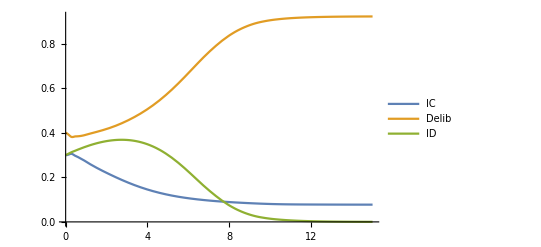

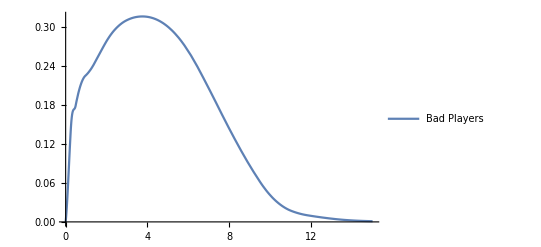

-Graphics-

```mathematica
c=1;
b=2;
Clear[g]

payoffIC:=-c+b*(x[t]+z[t]);
payoffID:=b*(x[t]+z[t]*goodID);
payoffDD:=-c*g[t]+b*(x[t]+z[t]);

goodIC:=1;
goodID:=y[t]*(1-g[t]);
goodDD:=1;

replicatorIC=x'[t]==x[t]*(payoffIC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD));
replicatorID=y'[t]==y[t]*(payoffID-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD));
replicatorDD=z'[t]==z[t]*(payoffDD-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD));
replicatorG=g'[t]==y[t]*goodID+z[t]+x[t] - g[t];

(*Solve the system of ODEs*)
solution=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorG,x[0]==0.3,y[0]==0.3,z[0]==0.4,g[0]==1},{x,y,z,g},{t,0,500},PrecisionGoal->0];
vectorField=Table[Flatten@{x[t]/. solution,y[t]/. solution,z[t]/. solution},{t,0,500,0.1}];
solution1=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorG,x[0]==0.2,y[0]==0.2,z[0]==0.6,g[0]==1},{x,y,z,g},{t,0,500},PrecisionGoal->0];
vectorFieldA = Table[Flatten@{x[t]/. solution1,y[t]/. solution1,z[t]/. solution1},{t,0,500,0.1}];
solution2=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorG,x[0]==0,y[0]==0.5,z[0]==0.5,g[0]==1},{x,y,z,g},{t,0,500},PrecisionGoal->0];
vectorFieldB = Table[Flatten@{x[t]/. solution2,y[t]/. solution2,z[t]/. solution2},{t,0,20,0.1}];
solution3=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorG,x[0]==0.1,y[0]==0.4,z[0]==0.5,g[0]==1},{x,y,z,g},{t,0,500},PrecisionGoal->0];
vectorFieldC = Table[Flatten@{x[t]/. solution3,y[t]/. solution3,z[t]/. solution2},{t,0,20,0.1}];
vectorFieldD=Table[Flatten@{x[t]/. solution,y[t]/. solution, z[t]/. solution},{t,0,500,0.1}];

Plot[Evaluate[{x[t],z[t],y[t]}/. solution],{t,0,100},PlotLegends->{"IC","Delib","ID"}]
Plot[Evaluate[{x[t],z[t],y[t]}/. solution],{t,0,15},PlotLegends->{"IC","Delib","ID"}]
Plot[Evaluate[{1-g[t]}/. solution],{t,0,15},PlotLegends->{ "Bad Players"}]

TernaryListPlot[{vectorField, vectorFieldA, vectorFieldB, vectorFieldC},FrameLabel->{"IC","ID","DD"}, Epilog->{Red,PointSize@Large,Point[{0.3, 0.4, 0.3}]}]
```

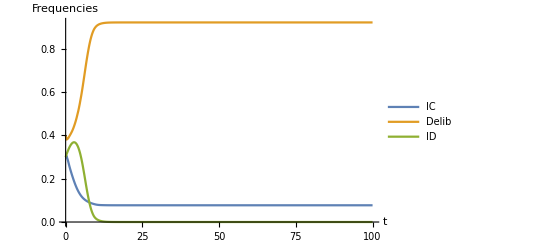

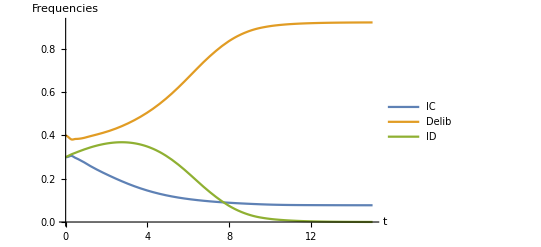

-Graphics-

```mathematica
(******************************************)
(*3 startegy game *)
c=1;
b=2;
Clear[g]

payoffIC:=-c+b*(x[t]+z[t]);
payoffID:=b*(x[t]+z[t]*(goodID));
payoffDD:=-c*g[t]+b*(x[t]+z[t]);

goodIC:=1;
goodID:=y[t]*(1-g[t]);
goodDD:=1;

replicatorIC=x'[t]==x[t]*(payoffIC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD));
replicatorID=y'[t]==y[t]*(payoffID-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD));
replicatorDD=z'[t]==z[t]*(payoffDD-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD));
replicatorG=g'[t]==y[t]*goodID+z[t]+x[t] - g[t];

(*Solve the system of ODEs*)
solution=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorG,x[0]==0.3,y[0]==0.3,z[0]==0.4,g[0]==1},{x,y,z,g},{t,0,500},PrecisionGoal->0];
vectorField=Table[Flatten@{x[t]/. solution,z[t]/. solution,y[t]/. solution},{t,0,500,0.1}];
Plot[Evaluate[{x[t],z[t],y[t]}/. solution],{t,0,100},PlotLegends->{"IC","Delib","ID"}, AxesLabel->{t, Frequencies}]
Plot[Evaluate[{x[t],z[t],y[t]}/. solution],{t,0,15},PlotLegends->{"IC","Delib","ID"}, AxesLabel->{t, Frequencies}]
```

```mathematica
(*****************************************)
```

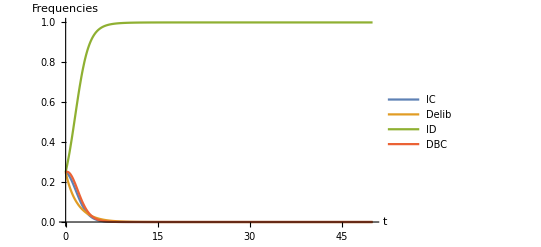

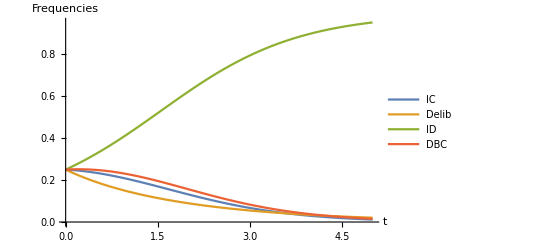

```mathematica
(*DBC only care about Deliberator or Intuitor, not reputation *)
c=1;
b=2;

payoffIC:=-c+b*(x[t]+z[t]+w[t]);
payoffID:=b*(x[t]+w[t]+z[t]*goodID);
payoffDD:=-c*g[t]+b*(x[t]+z[t]*goodDD+w[t]*(1-g[t]));
payoffGDBC:=-c*(x[t]+y[t]+z[t]*(1-g[t])+w[t])+b*(x[t]+z[t]*goodDBC+w[t]);
goodIC:=1;
goodID:=y[t]/(1+y[t]);
goodDD:=1;
goodDBC:=1-(z[t]*g[t]);

replicatorIC=x'[t]==x[t]*(payoffIC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorID=y'[t]==y[t]*(payoffID-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDD=z'[t]==z[t]*(payoffDD-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDBC=w'[t]==w[t]*(payoffGDBC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorG=g'[t]==w[t]*goodDBC+z[t]+x[t] +((y[t])^2)/(1+y[t])- g[t];


(*Solve the system of ODEs*)
solution=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorDBC,replicatorG,x[0]==0.25,y[0]==0.25,z[0]==0.25,w[0]==0.25, g[0]==1},{x,y,z,w, g},{t,0,500}];
vectorField=Table[Flatten@{x[t]/. solution,z[t]/. solution,y[t]/. solution,w[t]/. solution},{t,0,500,0.1}];
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,50},PlotLegends->{"IC","Delib","ID","DBC"}, AxesLabel->{"t", "Frequencies"}]
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,5},PlotLegends->{"IC","Delib","ID","DBC"}, AxesLabel->{"t", "Frequencies"}]
```

```mathematica
(*****************************************)
```

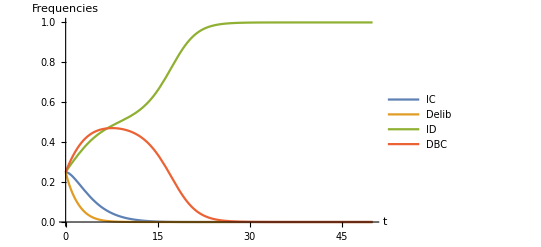

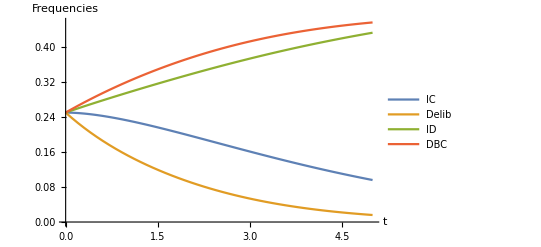

```mathematica
(*all 4 strategies but DBC takes reputation into account aswell*)
c=1;
b=2;

payoffIC:=-c+b*(x[t]+z[t]+w[t]);
payoffID:=b*(x[t]+w[t]*goodID+z[t]*goodID);
payoffDD:=-c*g[t]+b*(x[t]+z[t]*goodDD+w[t]*(1-g[t]));
payoffGDBC:=-c*(x[t]+y[t]*(goodID)+z[t]*(1-g[t])+w[t])+b*(x[t]+z[t]*goodDBC+w[t]);
goodIC:=1;
goodID:=y[t]/(1+y[t]);
goodDD:=1;
goodDBC:=1-(z[t]*g[t]);

replicatorIC=x'[t]==x[t]*(payoffIC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorID=y'[t]==y[t]*(payoffID-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDD=z'[t]==z[t]*(payoffDD-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDBC=w'[t]==w[t]*(payoffGDBC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorG=g'[t]==w[t]*goodDBC+z[t]+x[t] +((y[t])^2)/(1+y[t])- g[t];


(*Solve the system of ODEs*)
solution=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorDBC,replicatorG,x[0]==0.25,y[0]==0.25,z[0]==0.25,w[0]==0.25, g[0]==1},{x,y,z,w, g},{t,0,500}];
vectorField=Table[Flatten@{x[t]/. solution,z[t]/. solution,y[t]/. solution,w[t]/. solution},{t,0,500,0.1}];
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,50},PlotLegends->{"IC","Delib","ID","DBC"}, AxesLabel->{"t", "Frequencies"}]
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,5},PlotLegends->{"IC","Delib","ID","DBC"}, AxesLabel->{"t", "Frequencies"}]
```

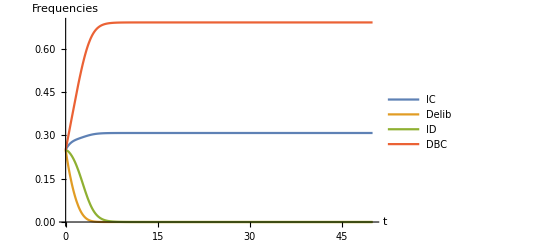

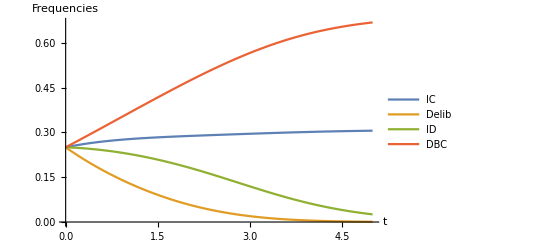

```mathematica
(*****************************************)
(*all 4 strategies but DBC takes reputation into account aswell, b =3*)
c=1;
b=3;

payoffIC:=-c+b*(x[t]+z[t]+w[t]);
payoffID:=b*(x[t]+w[t]*goodID+z[t]*goodID);
payoffDD:=-c*g[t]+b*(x[t]+z[t]*goodDD+w[t]*(1-g[t]));
payoffGDBC:=-c*(x[t]+y[t]*(goodID)+z[t]*(1-g[t])+w[t])+b*(x[t]+z[t]*goodDBC+w[t]);
goodIC:=1;
goodID:=y[t]/(1+y[t]);
goodDD:=1;
goodDBC:=1-(z[t]*g[t]);

replicatorIC=x'[t]==x[t]*(payoffIC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorID=y'[t]==y[t]*(payoffID-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDD=z'[t]==z[t]*(payoffDD-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDBC=w'[t]==w[t]*(payoffGDBC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorG=g'[t]==w[t]*goodDBC+z[t]+x[t] +((y[t])^2)/(1+y[t])- g[t];


(*Solve the system of ODEs*)
solution=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorDBC,replicatorG,x[0]==0.25,y[0]==0.25,z[0]==0.25,w[0]==0.25, g[0]==1},{x,y,z,w, g},{t,0,500}];
vectorField=Table[Flatten@{x[t]/. solution,z[t]/. solution,y[t]/. solution,w[t]/. solution},{t,0,500,0.1}];
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,50},PlotLegends->{"IC","Delib","ID","DBC"}, AxesLabel->{"t", "Frequencies"}]
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,5},PlotLegends->{"IC","Delib","ID","DBC"}, AxesLabel->{"t", "Frequencies"}]
```

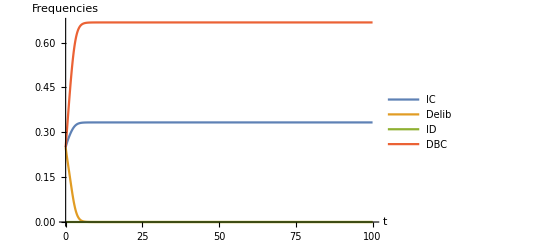

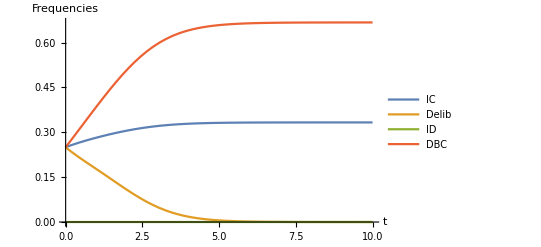

```mathematica
(*phase graphs*)
(* No Defectors*)
Clear[g]
c=1;
b=2;

payoffIC:=-c+b*(x[t]+z[t]+w[t]);
payoffID:=0;
payoffDD:=-c*g[t]+b*(x[t]+z[t]*goodDD+w[t]*(1-g[t]));
payoffGDBC:=-c*(x[t]+y[t]+z[t]*(1-g[t])+w[t])+b*(x[t]+z[t]*goodDBC+w[t]);
goodIC:=1;
goodID:=y[t]/(1+y[t]);
goodDD:=1;
goodDBC:=1-z[t]*g[t];

replicatorIC=x'[t]==x[t]*(payoffIC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorID=y'[t]==y[t]*(payoffID-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDD=z'[t]==z[t]*(payoffDD-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDBC=w'[t]==w[t]*(payoffGDBC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorG=g'[t]==w[t]*goodDBC+z[t]+x[t] +((y[t])^2)/(1+y[t])- g[t];


(*Solve the system of ODEs*)
solution=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorDBC,replicatorG,x[0]==0.25,y[0]==0,z[0]==0.25,w[0]==0.25, g[0]==1},{x,y,z,w, g},{t,0,500}];
vectorField=Table[Flatten@{x[t]/. solution,z[t]/. solution,y[t]/. solution,w[t]/. solution},{t,0,500,0.1}];
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,100},PlotLegends->{"IC","Delib","ID","DBC"}, AxesLabel->{"t", "Frequencies"}]
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,10},PlotLegends->{"IC","Delib","ID","DBC"}, AxesLabel->{"t", "Frequencies"}]
```

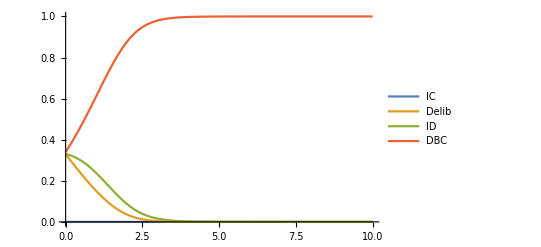

```mathematica
(*****************************************)
(*No Cooperators  *)
c=1;
b=3;

payoffIC:=-c+b*(x[t]+z[t]+w[t]);
payoffID:=b*(x[t]+w[t]*goodID+z[t]*goodID);
payoffDD:=-c*g[t]+b*(x[t]+z[t]*goodDD+w[t]*(1-g[t]));
payoffGDBC:=-c*(x[t]+y[t]*(goodID)+z[t]*(1-g[t])+w[t])+b*(x[t]+z[t]*goodDBC+w[t]);
goodIC:=1;
goodID:=y[t]/(1+y[t]);
goodDD:=1;
goodDBC:=1-(z[t]*g[t]);

replicatorIC=x'[t]==x[t]*(payoffIC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorID=y'[t]==y[t]*(payoffID-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDD=z'[t]==z[t]*(payoffDD-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDBC=w'[t]==w[t]*(payoffGDBC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorG=g'[t]==w[t]*goodDBC+z[t]+x[t] +((y[t])^2)/(1+y[t])- g[t];


(*Solve the system of ODEs*)
solution=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorDBC,replicatorG,x[0]==0,y[0]==0.33,z[0]==0.33,w[0]==0.34, g[0]==1},{x,y,z,w, g},{t,0,500}];
vectorField=Table[Flatten@{x[t]/. solution,z[t]/. solution,y[t]/. solution,w[t]/. solution},{t,0,500,0.1}];
vectorField
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,10},PlotLegends->{"IC","Delib","ID","DBC"}]
```

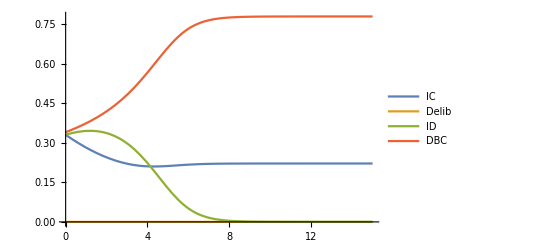

```mathematica
(**********************************************)
(*No Deliberators *)
c=1;
b=3;

payoffIC:=-c+b*(x[t]+z[t]+w[t]);
payoffID:=b*(x[t]+w[t]*goodID+z[t]*goodID);
payoffDD:=-c*g[t]+b*(x[t]+z[t]*goodDD+w[t]*(1-g[t]));
payoffGDBC:=-c*(x[t]+y[t]*(goodID)+z[t]*(1-g[t])+w[t])+b*(x[t]+z[t]*goodDBC+w[t]);
goodIC:=1;
goodID:=y[t]/(1+y[t]);
goodDD:=1;
goodDBC:=1-(z[t]*g[t]);

replicatorIC=x'[t]==x[t]*(payoffIC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorID=y'[t]==y[t]*(payoffID-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDD=z'[t]==z[t]*(payoffDD-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorDBC=w'[t]==w[t]*(payoffGDBC-(x[t]*payoffIC+y[t]*payoffID+z[t]*payoffDD+w[t]*payoffGDBC));
replicatorG=g'[t]==w[t]*goodDBC+z[t]+x[t] +((y[t])^2)/(1+y[t])- g[t];



(*Solve the system of ODEs*)
solution=NDSolve[{replicatorIC,replicatorID,replicatorDD,replicatorDBC,replicatorG,x[0]==0.33,y[0]==0.33,z[0]==0,w[0]==0.34, g[0]==1},{x,y,z,w, g},{t,0,500}];
vectorField=Table[Flatten@{x[t]/. solution,z[t]/. solution,y[t]/. solution,w[t]/. solution},{t,0,500,0.1}];
vectorField1=Table[Flatten@{x[t]/. solution,y[t]/. solution,w[t]/. solution},{t,0,500,0.1}];
Plot[Evaluate[{x[t],z[t],y[t],w[t]}/. solution],{t,0,15},PlotLegends->{"IC","Delib","ID","DBC", "Good"}]
```